# Mathematica for Bioinformatics

by George I. Mias, PhD
["http://georgemias.org"](http://georgemias.org)

Cite this chapter as:
Mias G. (2018) Graphs and Networks. In: Mathematica for Bioinformatics. Springer, Cham. https://doi.org/10.1007/978-3-319-72377-8_10

## Chapter 10: Networks

## Introduction to Graphs

### Vertices and Edges

We can think of a graph, G, as comprised of two sets of two sets : (i) Vertices, V,  which are the nodes of the graph, and (ii) Edges, E, which are the links or connections between vertices .



```mathematica
Graph[{1<->2}]
```

This is an example of an undirected edge. There are multiple ways to input this in the Wolfram Language. You may find the edge symbol a bit  tricky to enter,  you can type, for undirected edges:
(i)  vertex_1 Esc ue Esc vertex_2
(ii) vertex_1  “\” “[UndirectedEdge]” vertex_2
(iii) use the input form UndirectedEdge[vertex_1, vertex_2].

```mathematica
Graph[{1<->2},PlotTheme->"ClassicDiagram"]
```

-Graphics-

The edges can also be directed, i.e. have a directionality from one vertex to another. These directed edges are provided in a different format: For example we have two vertices 1,2 where we have a directed edge from 1 to 2:

```mathematica
Graph[{1->2},PlotTheme->"ClassicDiagram"]
```

-Graphics-

To enter directed edges as symbols you can enter:
(i)  vertex_1 Esc de Esc vertex_2
(ii) vertex_1  “\” “[DirectedEdge]” vertex_2
(iii) use the input form DirectedEdge[vertex_1, vertex_2].

```mathematica
simpleGraphExample=Graph[
{1->2,2<->3,3-> 4,2-> 4,2-> 5,
3-> 5,5<->1},PlotTheme->"ClassicDiagram"]
```

-Graphics-

```mathematica
simpleGraphExample7=Graph[{1,2,3,4,5,6,7},
{1->2,2<->3,3-> 4,2-> 4,2-> 5,3-> 5,5<->1},
PlotTheme->"ClassicDiagram"]
```

-Graphics-

```mathematica
SystemOpen["paclet:example/VisualizeEulerianCycles"] (* the figure is available in the Documentation Center*)
```

```mathematica
sevenBridges=Graph[{UndirectedEdge[1,2],
 UndirectedEdge[1,2], UndirectedEdge[2, 3],
UndirectedEdge[2, 3], UndirectedEdge[2,4],
 UndirectedEdge[3,4],UndirectedEdge[1, 4]},
PlotTheme->"ClassicDiagram"]
```

-Graphics-

```mathematica
EulerianGraphQ[sevenBridges]
```

False

## Basic Graph Construction

### Entering a Graph

```mathematica
vertexLabels=#-> Style[Subscript[ "V",
ToString[#]],FontFamily->"Arial",Bold]&/@Range[7]
```

{1→V_1,2→V_2,3→V_3,4→V_4,5→V_5,6→V_6,7→V_7}

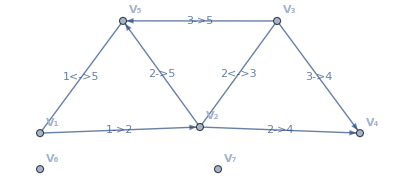

```mathematica
simpleGraphExample7Labeled=Graph[Range[7],
{1->2,2<->3,3-> 4,2-> 4,2-> 5,3-> 5,5<->1},
VertexLabels-> vertexLabels,
EdgeLabels->"Name"]
```

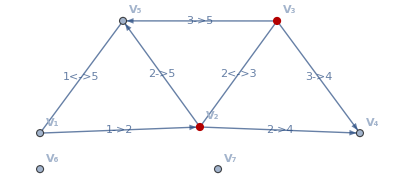

```mathematica
HighlightGraph[simpleGraphExample7Labeled,{2,3}]
```

Graph vertices can actually be any object

```mathematica
verticesCentralDogma={"DNA","mRNA","Protein"};
edgesCentralDogma={DirectedEdge["DNA","mRNA"],
DirectedEdge["mRNA","Protein"]};
edgeLabelsCentralDogma={DirectedEdge["DNA","mRNA"]->
Labeled["DNA to mRNA","Transcription"],
DirectedEdge["mRNA","Protein"]-> 
Labeled["mRNA to Protein", "Translation"]};
```

```mathematica
centralDogmaGraph=Graph[verticesCentralDogma,
edgesCentralDogma,
VertexSize-> 0.3,
PlotTheme->"ClassicDiagram",
EdgeLabels->edgeLabelsCentralDogma]
```

-Graphics-

```mathematica
VertexList[centralDogmaGraph]
```

{DNA,mRNA,Protein}

```mathematica
VertexIndex[centralDogmaGraph,"Protein"]
```

3

```mathematica
EdgeList[centralDogmaGraph]
```

{DNA->mRNA,mRNA->Protein}

```mathematica
EdgeIndex[centralDogmaGraph,"mRNA"->"Protein"]
```

2

```mathematica
VertexIndex[centralDogmaGraph,"DNA"]
```

1

```mathematica
EdgeDelete[simpleGraphExample7,2->  5]
(*Can also input as 
EdgeDelete[simpleGraphExample,DirectedEdge[2,5]]*)
```

-Graphics-

```mathematica
EdgeAdd[simpleGraphExample7,1<->3]
```

-Graphics-

```mathematica
VertexDelete[simpleGraphExample7,1]
```

-Graphics-

```mathematica
VertexAdd[simpleGraphExample7,8]
```

-Graphics-

```mathematica
graphPlot=GraphPlot[simpleGraphExample7]
```

-Graphics-

```mathematica
Head[graphPlot]
```

Graphics

```mathematica
Head[simpleGraphExample]
```

Graph

### Defining Weighted Graphs

```mathematica
edgeWeights= {2,3,1,6,1,2,1};
```

```mathematica
simpleGraphExampleWeightedEdges=
Graph[{1->2,2<->3,3-> 4,2-> 4,
2-> 5,3-> 5,5<->1},
EdgeWeight-> edgeWeights,
PlotTheme->"ClassicDiagram"];simpleGraphExampleWeightedEdges
```

-Graphics-

```mathematica
Graph[{1->2,2<->3,3-> 4,2-> 4,2-> 5,
3-> 5,5<->1},
EdgeWeight-> edgeWeights,
PlotTheme->"ClassicDiagram",
EdgeLabels->"EdgeWeight"]
```

-Graphics-

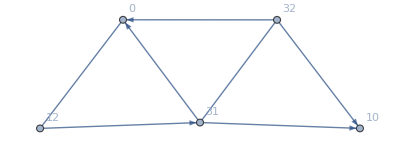

```mathematica
simpleGraphExampleWeightedVertices=
Graph[{1->2,2<->3,3-> 4,2-> 4,
2-> 5,3-> 5,5<->1},
VertexWeight-> {12,31,32,10,0},
VertexLabels-> "VertexWeight"]
```

## Basic Graph Properties

### Degree

We can calculate the degree for any vertex in a graph, which corresponds to the number of incident edges.

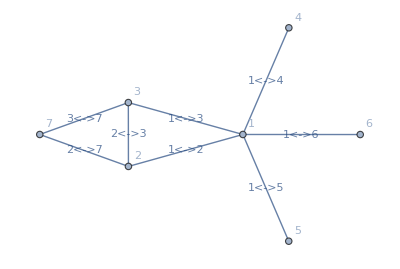

```mathematica
graphExample7VerticesEdges=
{1<-> 2,2<->3,3<->1,4<-> 1,5<-> 1,6<-> 1,
7<-> 2,7<-> 3};
graphExample7Vertices=
Graph[graphExample7VerticesEdges,
VertexLabels-> "Name",
EdgeLabels->"Name"]
```

We can then use VertexDegree to obtain all degrees for all vertices in the graph as a list :

```mathematica
VertexDegree[graphExample7Vertices]
```

{5,3,3,1,1,1,2}

Now let us consider a directed graph. The vertices can now have in-degree, which is the number of inbound incident edges, or out degree which is the number of outbound incident edges.

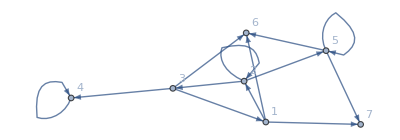

```mathematica
graphExampleLoopsDirectedEdges=
{1->2,2->3,2->2,3->1,3->4,4->4,2->5,
1->6,3->6,5->6,1->7,5->7,5->5};
graphExampleLoopsDirected=
Graph[graphExampleLoopsDirectedEdges,
VertexLabels-> "Name"]
```

```mathematica
VertexOutDegree[graphExampleLoopsDirected]
```

{3,3,3,1,3,0,0}

```mathematica
VertexInDegree[graphExampleLoopsDirected]
```

{1,2,1,2,2,3,2}

```mathematica
VertexDegree[graphExampleLoopsDirected]
```

{4,5,4,3,5,3,2}

### Adjacency Matrix

The adjacency matrix is a way to represent a graph in an array. In such a matrix with entries a_ij the rows and columns represent the vertices. Hence the matrix is square. If a graph is simple, which means it has no loops or multiple edges then the adjacency matrix entries take values 0 and 1, and the matrix is symmetric. A non-zero entry indicates that the vertices are adjacent (i.e. connected). In the Wolfram Language, the AdjacencyMatrix function is used to produce the matrices.

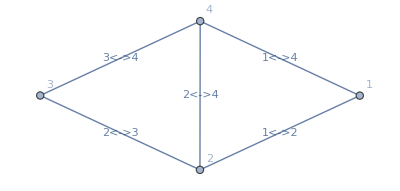

```mathematica
graphSimple=Graph[{1, 2, 3, 4},
 {UndirectedEdge[1, 2], UndirectedEdge[2, 3],
 UndirectedEdge[2, 4], UndirectedEdge[3, 4],
 UndirectedEdge[1, 4]},
VertexLabels->"Name",
EdgeLabels->"Name"]
```

```mathematica
adjGraphSimple=AdjacencyMatrix[graphSimple];
```

```mathematica
Head[adjGraphSimple]
```

SparseArray

```mathematica
adjGraphSimple["Properties"]
```

{AdjacencyLists,Background,BandWidth,ColumnIndices,Density,MatrixColumns,NonzeroValues,PatternArray,Properties,RowPointers}

```mathematica
adjGraphSimple//MatrixForm
```

(0 | 1 | 0 | 1
1 | 0 | 1 | 1
0 | 1 | 0 | 1
1 | 1 | 1 | 0)

```mathematica
adjSevenBridges=AdjacencyMatrix[sevenBridges];
adjSevenBridges//MatrixForm
```

(0 | 2 | 0 | 1
2 | 0 | 2 | 1
0 | 2 | 0 | 1
1 | 1 | 1 | 0)

```mathematica
AdjacencyMatrix[Graph[graphExampleLoopsDirected]]//MatrixForm
```

(0 | 1 | 0 | 0 | 0 | 1 | 1
0 | 1 | 1 | 0 | 1 | 0 | 0
1 | 0 | 0 | 1 | 0 | 1 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0)

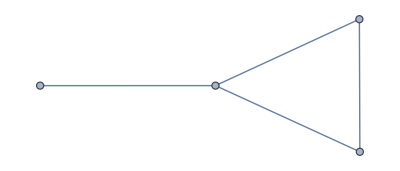

```mathematica
AdjacencyGraph[{{0,1,0,1},{1,0,1,1},
{0,1,0,0},{1,1,0,0}}]
```

### Weighted Adjacency Matrix

```mathematica
exampleWeightedAdjacencyMatrix=
WeightedAdjacencyMatrix[simpleGraphExampleWeightedEdges]//MatrixForm
```

(0 | 2 | 0 | 0 | 1
0 | 0 | 3 | 6 | 1
0 | 3 | 0 | 1 | 2
0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0)

```mathematica
AdjacencyMatrix[
simpleGraphExampleWeightedEdges]//
MatrixForm
```

(0 | 1 | 0 | 0 | 1
0 | 0 | 1 | 1 | 1
0 | 1 | 0 | 1 | 1
0 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0)

## Some More Definitions

### Walks and Paths

Walk: a walk on a graph is a sequence of vertices, {v_1,v_2,...,v_n} so that  all edges connecting sequential elements in the list are included.

Path: a path is a walk in which the list of vertices does not include duplicates - i.e. no vertex is visited twice.  In a connected graph any vertex in the graph has a path to any other vertex in the graph. A disconnected graph is a graph that is not connected (and will thus have graph parts disconnected from the rest)

Trail: a trail is a walk in which the edges are distinct (but the vertices do not have to be)

Cycle: a cycle is a path with an additional edge connecting the last to the first vertex (think of a circle closing on itself)

Geodesic: a geodesic is the shortest path that can be found connecting two vertices

Length: The length is defined in terms of the number of edges in any of the above.

```mathematica
shortestPath7Vertices=FindShortestPath[graphExample7Vertices,1,7]
```

{1,2,7}

```mathematica
shortestPathGraph=PathGraph[shortestPath7Vertices];
```

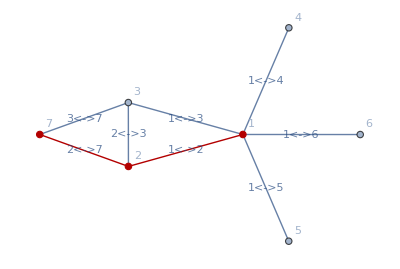

```mathematica
HighlightGraph[graphExample7Vertices,shortestPathGraph]
```

### Graph Geometry

Eccentricity: the eccentricity,ϵ of a vertex is the maximum shortest path between the given vertex and any other vertex. For any graph we can use the function VertexEccentricity[graph, vertex_i] to get he eccentricity. For example we extract all the eccentricities for thesevenBridges and simpleGraphExample graphs from above:

```mathematica
VertexEccentricity[sevenBridges,#]&/@VertexList[sevenBridges]
```

{2,1,2,1}

```mathematica
VertexEccentricity[graphExample7Vertices,#]&/@VertexList[graphExample7Vertices]
```

{2,2,2,3,3,3,3}

Graph Diameter: the graph diameter, d,  is the maximum eccentricity measured across all vertices of the graph. The set of all vertices with eccentricity equal to the diameter d is the periphery of the graph.

```mathematica
GraphDiameter[sevenBridges]
```

2

```mathematica
GraphDiameter[graphExample7Vertices]
```

3

Graph Radius: the graph radius, r,  is the minimum eccentricity measured across all vertices of the graph. Any vertex is called central if its eccentricity matches r, and the set of these central vertices is the center of the graph.

```mathematica
GraphRadius[sevenBridges]
```

1

```mathematica
GraphRadius[graphExample7Vertices]
```

2

### Centrality

Degree Centrality: For a given vertex, we can think of it as being important the higher its degree. DegreeCentrality can calculate the measure for all vertices in a graph:

```mathematica
DegreeCentrality[graphExample7Vertices]
```

{5,3,3,1,1,1,2}

Betweenness Centrality: We can calculate the betweenness centrality of a vertex in a graph. This is defined as the number of shortest paths between vertex pairs that pass through the vertex.  It measures the numbers of vertex pair sets that essentially go through the vertex to connect to each other. For our previous example we get:

```mathematica
BetweennessCentrality[graphExample7Vertices]
```

{12.,2.,2.,0.,0.,0.,0.}

```mathematica
scaledBetweenness=Rescale[BetweennessCentrality[graphExample7Vertices]]
```

{1.,0.166667,0.166667,0.,0.,0.,0.}

```mathematica
vertexListExample7=VertexList[graphExample7Vertices];
```

```mathematica
HighlightGraph[graphExample7Vertices,vertexListExample7,VertexSize-> Thread[vertexListExample7-> scaledBetweenness]]
```

-Graphics-

### Clustering Coefficient

#### Local Clustering Coefficient

We may went to measure the interconnectedness of neighbors of a vertex. The local clustering coefficient for a vertex is the probability that a given pair of neighbors to a vertex are themselves neighbors (i.e. connected). It is measured as the ratio (pairs of connected neighbors of the vertex)/  (all neighbor vertex pairs for the vertex).

```mathematica
localClusteringExample7=LocalClusteringCoefficient[graphExample7Vertices]
```

{1/10,2/3,2/3,0,0,0,1}

```mathematica
HighlightGraph[graphExample7Vertices,vertexListExample7,VertexSize-> Thread[vertexListExample7-> localClusteringExample7]]
```

-Graphics-

#### Global Clustering Coefficient

The GlobalClusteringCoefficient function gives us the global clustering coefficient,  measuring the fraction (number of closed triplets)/(number of all triplets). Triplets are sets of 3 nodes that are either open (connected by two edges) or closed (connected by three edges -- i.e. triangles).

```mathematica
GlobalClusteringCoefficient[graphExample7Vertices]
```

6/17

## Graph Examples

There are many graphs that can be created through named commands in the Wolfram Language. See (guide/GraphConstructionAndRepresentation). The Wolfram Language additionally has many available theoretical and empirical graphs that are available through GraphData and ExampleData respectively. We first go through a few definitions, and then  look at a few examples in this section, that are often used in graph analysis.

### Empty Graphs

```mathematica
emptyGraphs=Graph[GraphData[{"Empty",#}],VertexSize-> Medium,PlotLabel->Style[Subscript["E",#],Italic,Bold]] &/@ Range[5];
```

```mathematica
gridGraphs[x_]:=Grid[{x},Dividers->Center,Frame-> True, FrameStyle->Directive[Dashing[4],Thickness[2],Opacity[0.3]]]
```

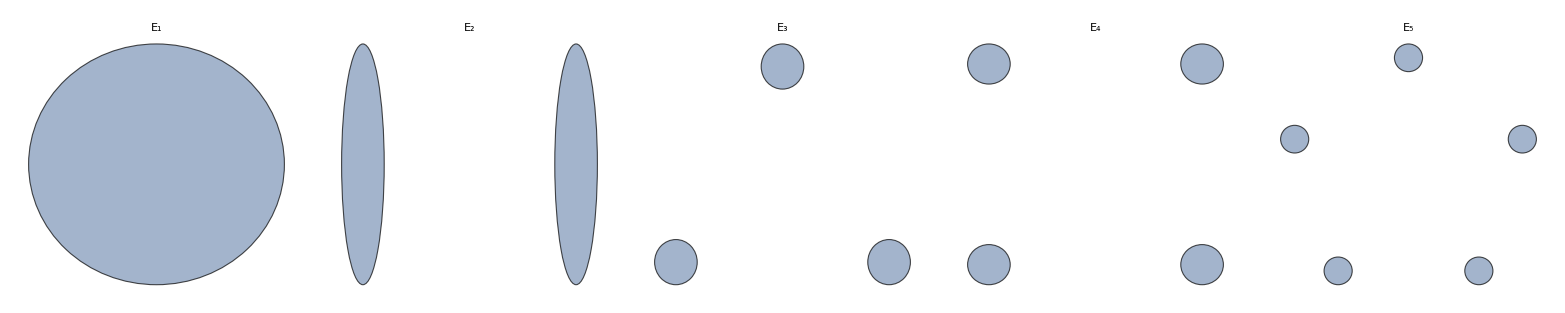

```mathematica
gridGraphs[emptyGraphs]
```

### Complete Graphs

A Complete Graph K_nhas n vertices that are all connected to each other. The function CompleteGraph generates the nth graph:

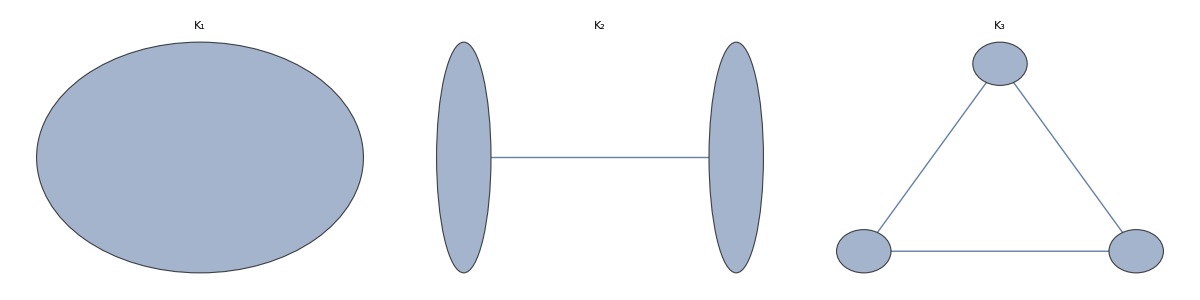

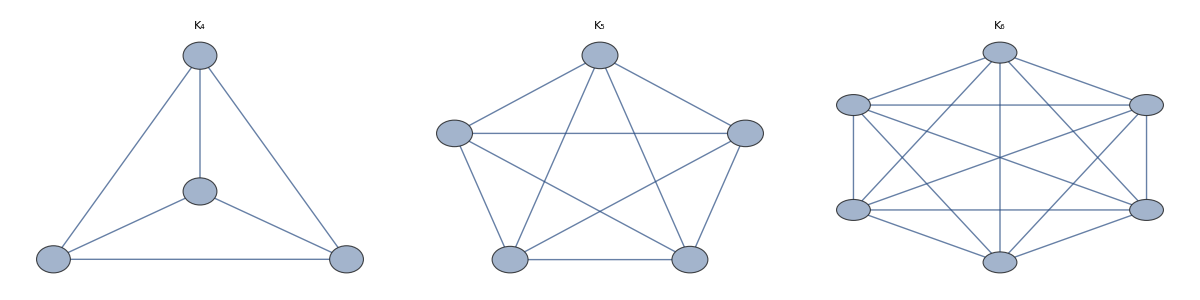

```mathematica
completeGraphs=CompleteGraph[#,
PlotLabel->
Style[Subscript["K",#],Italic,Bold],
VertexSize-> Medium,
EdgeStyle-> Automatic]&/@ Range[7];
gridGraphs[completeGraphs[[1;;3]]]
gridGraphs[completeGraphs[[4;;6]]]
```

```mathematica
MatrixForm@AdjacencyMatrix[#]&/@completeGraphs
```

{(0),(0 | 1
1 | 0),(0 | 1 | 1
1 | 0 | 1
1 | 1 | 0),(0 | 1 | 1 | 1
1 | 0 | 1 | 1
1 | 1 | 0 | 1
1 | 1 | 1 | 0),(0 | 1 | 1 | 1 | 1
1 | 0 | 1 | 1 | 1
1 | 1 | 0 | 1 | 1
1 | 1 | 1 | 0 | 1
1 | 1 | 1 | 1 | 0),(0 | 1 | 1 | 1 | 1 | 1
1 | 0 | 1 | 1 | 1 | 1
1 | 1 | 0 | 1 | 1 | 1
1 | 1 | 1 | 0 | 1 | 1
1 | 1 | 1 | 1 | 0 | 1
1 | 1 | 1 | 1 | 1 | 0),(0 | 1 | 1 | 1 | 1 | 1 | 1
1 | 0 | 1 | 1 | 1 | 1 | 1
1 | 1 | 0 | 1 | 1 | 1 | 1
1 | 1 | 1 | 0 | 1 | 1 | 1
1 | 1 | 1 | 1 | 0 | 1 | 1
1 | 1 | 1 | 1 | 1 | 0 | 1
1 | 1 | 1 | 1 | 1 | 1 | 0)}

```mathematica
BetweennessCentrality[#]&/@completeGraphs
```

{{0.},{0.,0.},{0.,0.,0.},{0.,0.,0.,0.},{0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.}}

```mathematica
DegreeCentrality[#]&/@completeGraphs
```

{{0},{1,1},{2,2,2},{3,3,3,3},{4,4,4,4,4},{5,5,5,5,5,5},{6,6,6,6,6,6,6}}

### Regular Graphs.

A regular graph has every vertex having the same degree. There are many named examples in GraphData

```mathematica
Length@GraphData["Regular"]
```

5721

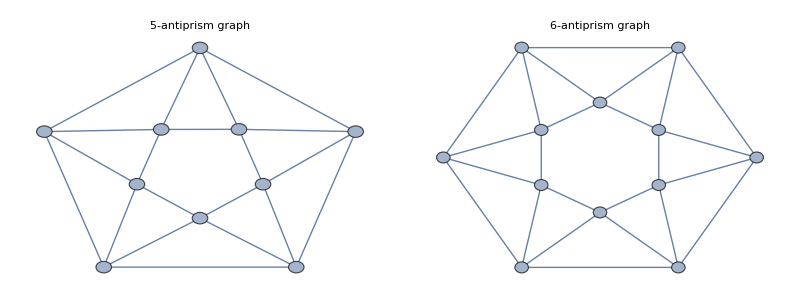

```mathematica
regularGraphs=Graph[GraphData[{"Antiprism",#}],
VertexSize-> Medium,
PlotLabel->
TextCell[GraphData[{"Antiprism",#},
"Name"]]] &/@ Range[5,6];
gridGraphs[regularGraphs]
```

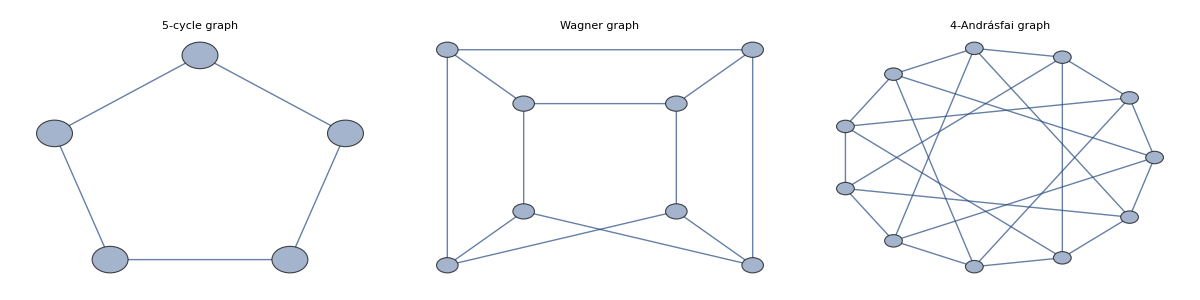

```mathematica
regularGraphs2=Graph[GraphData[{"Andrasfai",#}],
VertexSize-> Medium,
PlotLabel->TextCell[GraphData[{"Andrasfai",#},
"Name"]]] &/@ Range[2,4];
gridGraphs[regularGraphs2]
```

```mathematica
GraphData[{"Andrasfai",2},"Properties"]//Short
```

{Acyclic,AdjacencyLists,«567»,ZeroSymmetric,ZeroTwo}

```mathematica
GraphData[{"Andrasfai",2},{"VertexCount","EdgeCount","EdgeBetweennessCentralities","DegreeSequence"}]
```

{5,5,{6,6,6,6,6},{2,2,2,2,2}}

```mathematica
MatrixForm[#]&/@GraphData[{"Andrasfai",3},{"AdjacencyMatrix"}]
```

{(0 | 1 | 0 | 0 | 1 | 0 | 0 | 1
1 | 0 | 1 | 0 | 0 | 1 | 0 | 0
0 | 1 | 0 | 1 | 0 | 0 | 1 | 0
0 | 0 | 1 | 0 | 1 | 0 | 0 | 1
1 | 0 | 0 | 1 | 0 | 1 | 0 | 0
0 | 1 | 0 | 0 | 1 | 0 | 1 | 0
0 | 0 | 1 | 0 | 0 | 1 | 0 | 1
1 | 0 | 0 | 1 | 0 | 0 | 1 | 0)}

### Cycle Graphs

We can look at various cycle graphs, C_i using CycleGraph. The CycleGraph takes as input the number of vertices. Also, we can define whether or not we want directed versions, by setting the option DirectedEdges to True

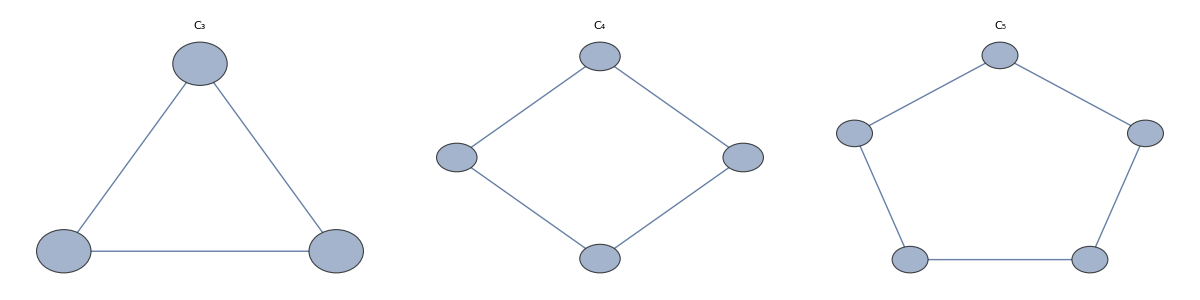

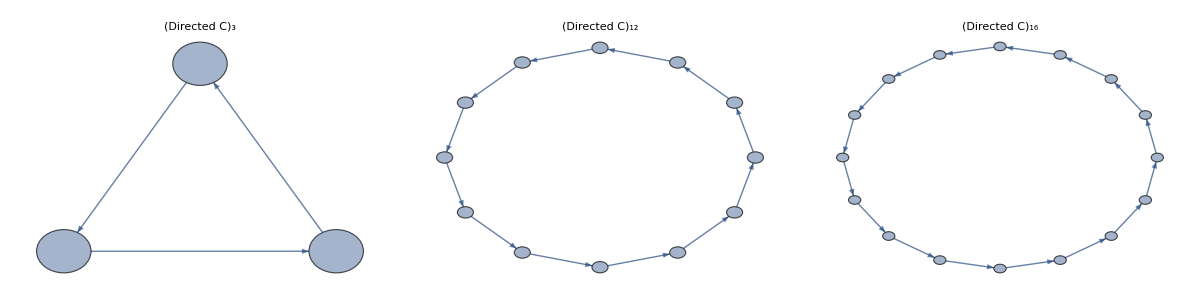

```mathematica
cycleGraphs={CycleGraph[#,VertexSize-> Medium,
PlotLabel->
Style[Subscript["C",#],Italic,Bold]] &/@
 Range[3,5],CycleGraph[#,VertexSize-> Medium,
PlotLabel->
Style[Subscript["Directed C",#],Italic,Bold],
DirectedEdges->True]&/@ {3,12,16} };
gridGraphs[cycleGraphs[[1]]]
gridGraphs[cycleGraphs[[2]]]
```

```mathematica
(Subscript["C",#]->MatrixForm[ AdjacencyMatrix[CycleGraph[#]]]&/@{3,5,10})
```

{C_3→(0 | 1 | 1
1 | 0 | 1
1 | 1 | 0),C_5→(0 | 1 | 0 | 0 | 1
1 | 0 | 1 | 0 | 0
0 | 1 | 0 | 1 | 0
0 | 0 | 1 | 0 | 1
1 | 0 | 0 | 1 | 0),C_10→(0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1
1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0)}

There are 1s in the off diagonals of the adjacency matrices (i.e. either side of the diagonal entry), representing an entry’s connection to its neighbor, and there is a one in the right and left corner, representing the connection between the start and end vertices.

### Trees

A tree is a connected graph that has no cycles.  Vertices of the tree with degree one are called leaves. There are for example Banana Tree graphs defined in GraphData:

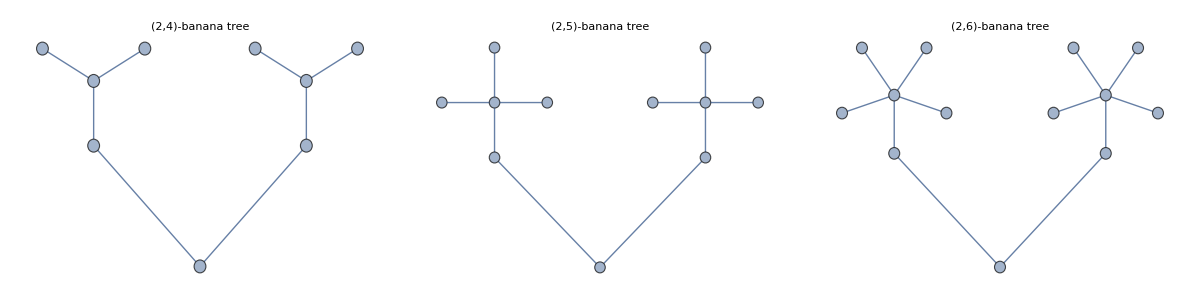

```mathematica
treeGraphs=Graph[
GraphData[{"BananaTree",{2,#}}],
VertexSize-> Medium,PlotLabel->
TextCell[GraphData[{"BananaTree",{2,#}},
"Name"]]] &/@ Range[4,6];
gridGraphs[treeGraphs]
```

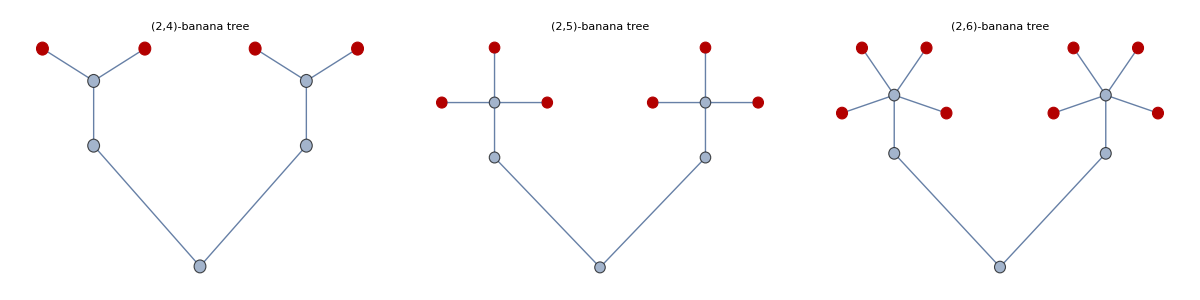

```mathematica
gridGraphs[HighlightGraph[#,GraphPeriphery[#]]&/@(treeGraphs)]
```

### Bipartite Graphs

In a bipartite graph the vertices can be split into two sets, so that every edge joins a vertex from one set to the other. Here are some examples of complete bipartite graphs that have 2 vertices in one set and varying numbers in the second set (4, 5 and 6):

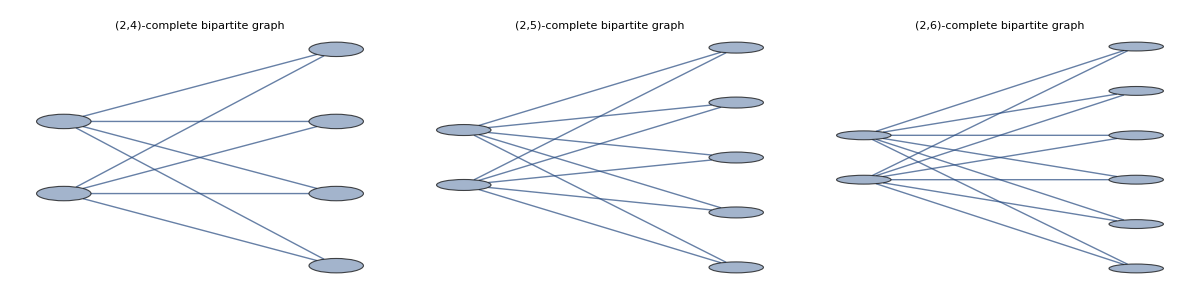

```mathematica
bipartiteGraphs=Graph[
GraphData[{"CompleteBipartite",{2,#}}],
VertexSize-> Medium,
PlotLabel->
TextCell[GraphData[{"CompleteBipartite",
{2,#}},"Name"]]] &/@ Range[4,6];
gridGraphs[bipartiteGraphs]
```

## Isomorphisms

Often we may have a different representation of two graphs, but they may in fact be in one-to-one correspondence, in that we can relabel the vertices and maintain the correspondence of edges. We can write this as: there exists f : V(G) → V(H), such that the edge u_j-v_j ∈ E(G) if and only if the edge f(u)-f(v) ∈ E(H).

Here is a simple example. Consider the following two graphs, 1 and 2:

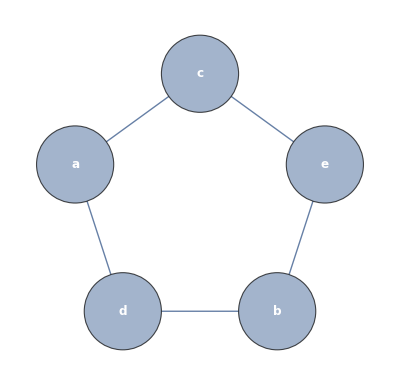
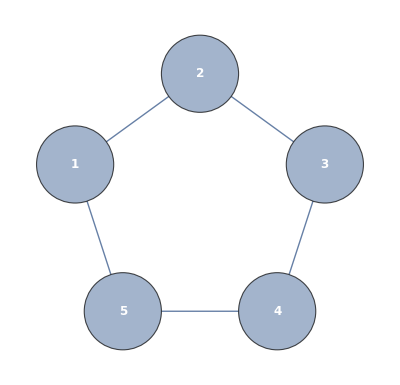
Graph1:-Graphics-Graph2:-Graphics-

```mathematica
graph1=Graph[
{"a","b","c","d","e"},
{"a"<-> "c","c"<->"e","e"<->"b","b"<->"d",
"d"<->"a"},
VertexSize->0.5,
VertexLabels-> Placed["Name",Center],
VertexLabelStyle->Directive[Bold,White,12],
VertexStyle->Thread[{"a","b","c","d","e"}->
{Red,Blue,Magenta,Orange,Purple}]];
graph2=CycleGraph[5,VertexSize->0.5,
VertexLabels-> Placed["Name",Center],VertexLabelStyle->Directive[Bold,White,12]];
Row[{"Graph1:",graph1,Spacer[40],
"Graph2:", graph2}]
```

```mathematica
IsomorphicGraphQ[graph1,graph2]
```

True

```mathematica
isomorphismG1G2=First@FindGraphIsomorphism[graph1,graph2]
```

<|a→1,b→3,c→5,d→2,e→4|>

```mathematica
Row@{graph1,Spacer[20],
Style[Column@Normal[isomorphismG1G2],
16,FontFamily->"Arial"],Spacer[20],
HighlightGraph[graph2, 
Style[isomorphismG1G2[#],
PropertyValue[{graph1,#},
VertexStyle]]&/@
VertexList[graph1]]}//TableForm
```

-Graphics-a→1
b→3
c→5
d→2
e→4-Graphics-

## Random Graphs

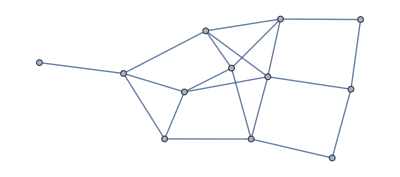

```mathematica
SeedRandom[7777];
RandomGraph[{12,20}]
```

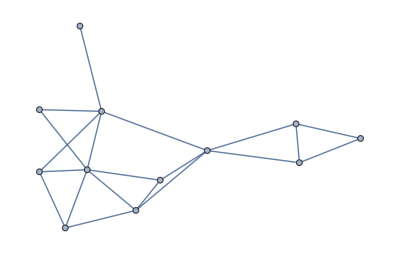
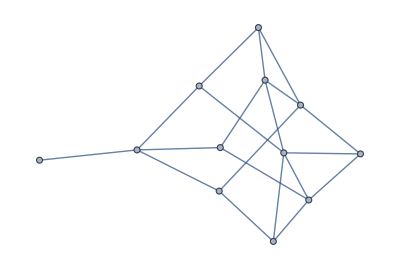
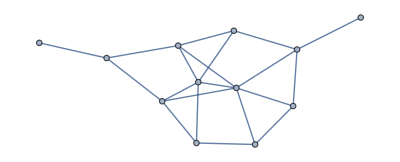
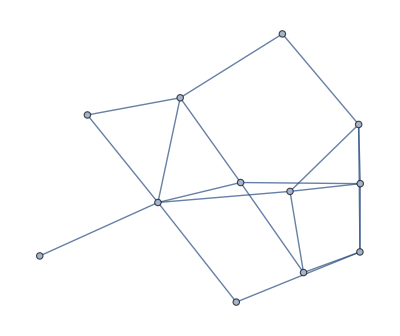
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
SeedRandom[7777];
RandomGraph[{12,20},5]
```

### Barabasi Albert Distribution

There are many random graph distributions that can be used to generate samples. For example, we can generate a Barabasi-Albert distribution for graphs with n vertices, in which an additional vertex with k edges is added at each step:

```mathematica
SeedRandom[7777];
barabasiAlbertRandomGraph=RandomGraph[BarabasiAlbertGraphDistribution[10^4,3]];
```

```mathematica
empiricalDistributionBarabasiAlbert=EmpiricalDistribution[VertexDegree[barabasiAlbertRandomGraph]];
```

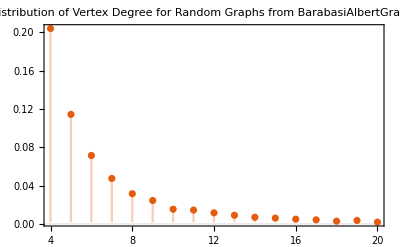

```mathematica
DiscretePlot[
PDF[empiricalDistributionBarabasiAlbert,i],
{i,4,20},
PlotRange-> 
All,PlotTheme-> "Scientific",PlotLabel->
"PDF of Empirical Distribution 
of Vertex Degree for Random Graphs 
from BarabasiAlbertGraphDistribution[10^4,3]]"]
```

### Watts Strogatz

In the Watts-Strogatz paper (Watts Strogatz, Nature 393, p40, 1998), the authors proposed a rewiring of a ring lattice (having n vertices and k edges per vertex) and randomly rewire each edge with probability p. In this way p can be tuned to lie between values of zero (which is order) and 1 (disorder).

```mathematica
?WattsStrogatzGraphDistribution
```

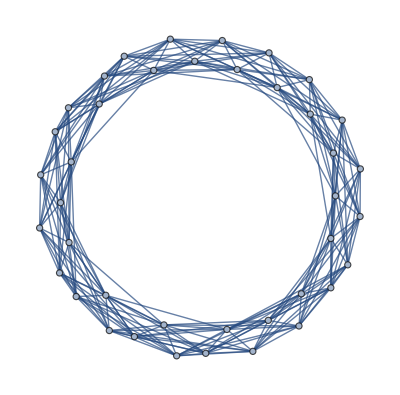
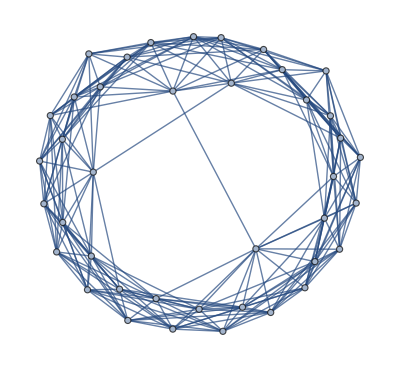
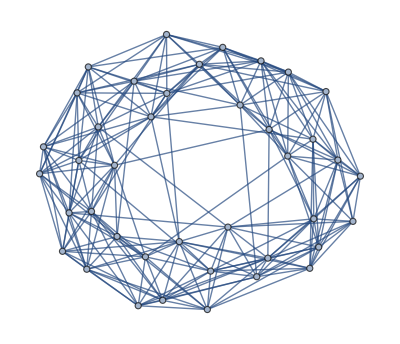
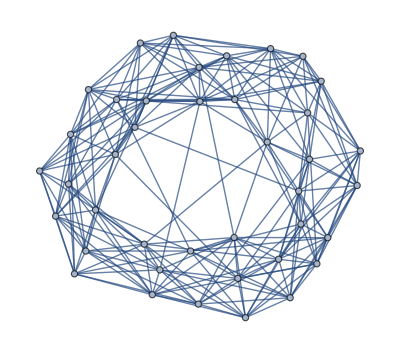
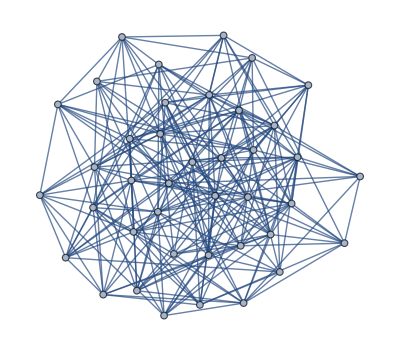
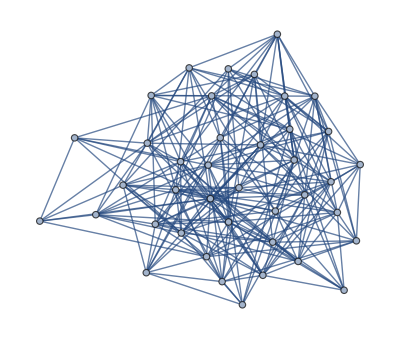

```mathematica
SeedRandom[2222];randomGraphsWattsStrogatz=
RandomGraph[
WattsStrogatzGraphDistribution[40,#,6]]&/@
{0.01,0.02,0.05,0.1,0.5,1}
```

```mathematica
empiricalDistributionsWattsStrogatz=
EmpiricalDistribution[
VertexDegree[#]]&/@randomGraphsWattsStrogatz;
```

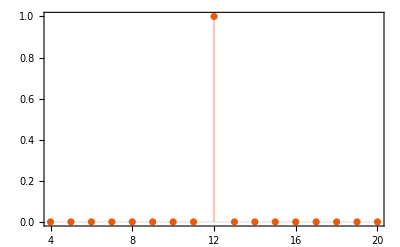
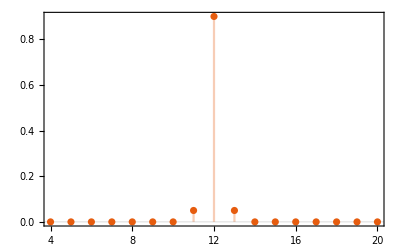
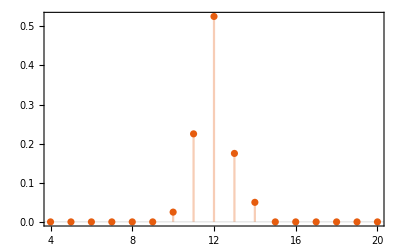
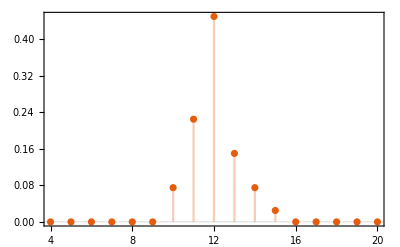
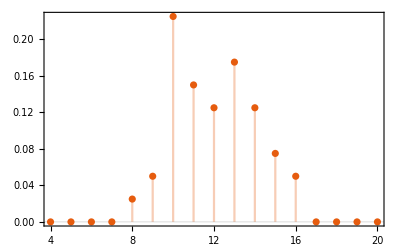
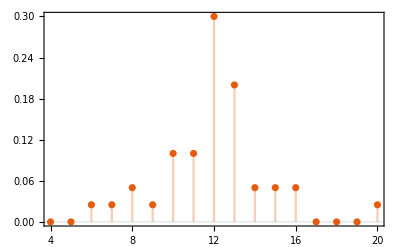

```mathematica
DiscretePlot[PDF[#,i],{i,4,20},
PlotRange-> All,PlotTheme-> "Scientific"]&/@
empiricalDistributionsWattsStrogatz
```